## Computing Butcher Coefficients

The goal is to compute the time offset, 𝒸, associated with the stages of a low storage RK integrator.  This is done by computing the Butcher table coefficients from the low storage coefficients following the algorithm in   https://doi.org/10.1016/j.jcp.2009.11.006

## 2S Method - α, β matrices

The sparse α, and β matrices are constructed according to Eqs 7 and 8 in the paper as well as the 3 recurrence relations specific to the 2S methods

```mathematica
βij[i_/;i<=1,j_]:=0
αij[i_/;i<=1,j_]:=0
δ[1]:=1
γ[i_/;i>=2,1]:= 1-γ[i,2]Sum[δ[j],{j,i-1}]
γ[2,2]:=1
βij[i_/;i>2, j_]:=-γ[i,2]βij[i-1,j]/γ[i-1,2]/;j==i-2
αij[i_/;i>2,j_]:=-γ[i,2]γ[i-1,1]/γ[i-1,2]/;j==i-2
αij[i_/;i>2,j_]:=1-αij[i,i-2]/;j==i-1
```

## Butcher table from α, β

```mathematica
butcher2S[m_]:=Module[{
α=SparseArray[{
{i_,j_}/;i==j+2->αij[i,j],
{i_,j_}/; i>2&&i==j+1->αij[i,j]
}, {m+1, m}],
β=SparseArray[{
{i_,j_}/;i==j+1->βij[i,j],
{i_,j_}/;i==j+2->βij[i,j]
},{m+1,m}],
α0,α1,β0,β1,A,b,c},
α0=α[[;;m,All]];
β0=β[[;;m,All]];
α1=α[[m+1;;,All]];
β1=β[[m+1;;,All]];
(* Equations 9a and 9b *);
A=Inverse[IdentityMatrix[m]-α0].β0;
b=Transpose[β1+α1.A][[All,1]];
c=Plus@@@A;
{A,b,c}]
```

## Low Storage coefficients for different schemes

```mathematica
scheme=<|
rk2-> {
m->2,
βij[2,1]->1,
βij[3,2]->1/2,
          γ[3,2]->1/2,
δ[2]->0
},
vl2->{
m->2,
βij[2,1]->1/2,
βij[3,2]->1,
	γ[3,2]->1,
δ[2]->0
},
rk3->{
m-> 3,
δ[2]->0,
δ[3]->0,
βij[2,1]->1,
βij[3,2]->1/4,
βij[4,3]->2/3,
γ[3,2]->3/4,
γ[4,2]->1/3
},
rk45->{
m->5,
γ[2,2]->1,
γ[3,2]->4.666545952121251,
γ[4,2]->0.964197464041912,
γ[5,2]-> -3.398279365655790,
γ[6,2]->0.229588412671583,
βij[2,1]->0.357534921136978,
βij[3,2]->2.364680399061355,
βij[4,3]->0.016239790859612,
βij[5,4]->0.498173799587251,
βij[6,5]->0.433334235669763,
δ[2]->0,
δ[3]->0,
δ[4]->0,
δ[5]->0,
δ[6]->0
}
|>;
```

## Make a Low-Storage RK method from coefficients

```mathematica
makeIntegrator[key_]:=Module[{
m=Key[key][scheme][[1]][[2]],
subs=Key[key][scheme][[2;;]],
butcher},
butcher=butcher2S[m]/.subs;
<|
beta->Table[βij[i,i-1],{i,2,m+1}]/.subs,
delta->Table[δ[i-1],{i,2,m+1}]/.subs,
gam0->Table[γ[i,1],{i,2,m+1}]/.subs,
gam1->Table[γ[i,2],{i,2,m+1}]/.subs,
c->butcher[[3]]
|>
]
rkInteriorStep[{s1_,s2_,time_, dt_,rhs_}, {beta_,gam0_,gam1_,delta_,c_}]:=
Module[{s2buf=s2+delta s1},
{gam0 s1+gam1 s2buf +beta dt rhs[s1,time+c dt ], s2buf, time, dt, rhs}]

rkStep[yn_,time_,dt_, rhs_,beta_,gam0_,gam1_,delta_,c_ ]:=
Fold[rkInteriorStep, {yn,0,time,dt,rhs}, Transpose[List[beta,gam0,gam1,delta,c]]]

rkIntegrate[y0_,t0_,tn_,dt_,rhs_,rkInfo_]:=Module[{
rkFunc=Function[{y,t},First[rkStep[y,t,dt,rhs,Key[beta][rkInfo],Key[gam0][rkInfo],Key[gam1][rkInfo],Key[delta][rkInfo],Key[c][rkInfo]]]]
},
Transpose[List[Range[t0,tn,dt],FoldList[rkFunc,y0,Range[t0,tn-dt,dt]]]]
]
```

Example:

```mathematica
makeIntegrator[rk45]
```

<|beta→{0.357535,2.36468,0.0162398,0.498174,0.433334},delta→{1,0,0,0,0},gam0→{0,-3.66655,0.0358025,4.39828,0.770412},gam1→{1,4.66655,0.964197,-3.39828,0.229588},c→{0,0.357535,1.05376,0.0539671,0.735536}|>

## Sanity Check

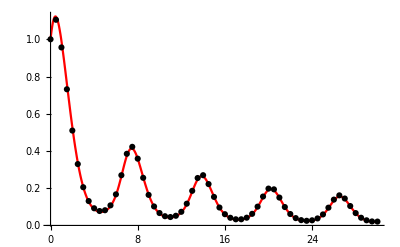

```mathematica
s=NDSolve[{y'[x]==y[x] Cos[y[x]+x],y[0]==1},y,{x,0,30}];
p1 = Plot[Evaluate[y[x]/.s],{x,0,30},PlotRange->All, PlotStyle->Red];
p2 = ListPlot[rkIntegrate[1,0,30,0.5,Function[{y,t},y Cos[t+y]],makeIntegrator[vl2]],PlotStyle->Black];
Show[p1,p2]
```

## Manufactured Solution

Chose a simple time-varying MS.  Chose an ODE whose r.h.s. is not a function of time.  This way all of the time information comes through the MS source term.  This seems like it should eliminate any fortuitous error cancellation from having the time dependence in multiple places?

```mathematica
(* y'= rhs[y,t] *)
rhs[y_,t_]:=y Cos[y] 
yMs[t_]:=1+Sin[t]/2
```

```mathematica
rkError[dt_,rkInfo_,levels_:3]:=Module[{
results=Table[rkIntegrate[yMs[0],0,200,dt/2^i,Function[{y,t},(D[yMs[x],x]/.x->t)-rhs[yMs[t],t]+rhs[y,t]],rkInfo ],{i,0,levels-1}],
errors,
linf
},
errors=Map[Function[{args},{args[[1]],Abs[args[[2]]-yMs[args[[1]]]]}],results,{2}];
Print[ListPlot/@errors];
linf=Map[Function[{err},Max[err[[All,2]]]]][errors];
(* Order of temporal convergence *);
Map[Log[2,#]&][linf[[1;;levels-1]]/linf[[2;;levels]]]
]
```

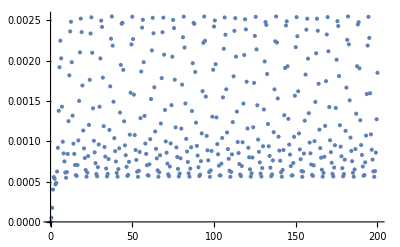
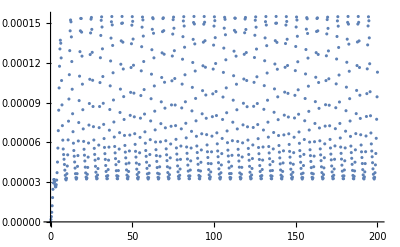
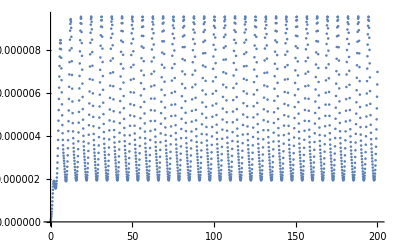
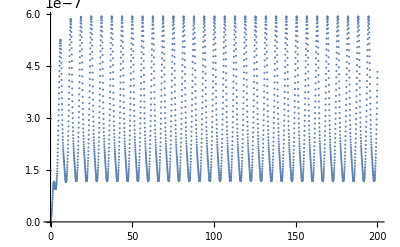

{4.04033,4.01988,4.01003}

```mathematica
rkError[0.5,makeIntegrator[rk45],4]
```

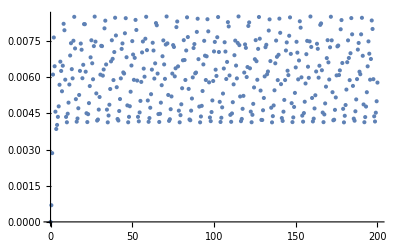
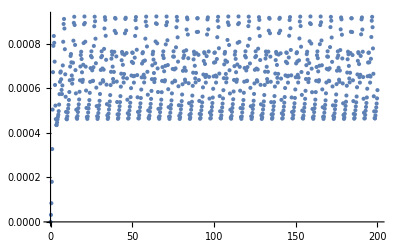
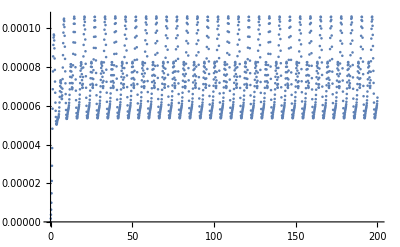
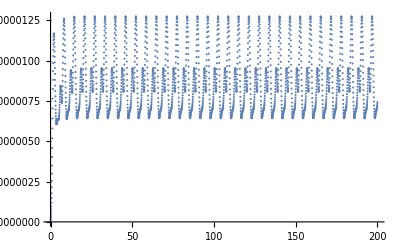

{3.20867,3.11738,3.06082}

```mathematica
rkError[0.5,makeIntegrator[rk3],4]
```

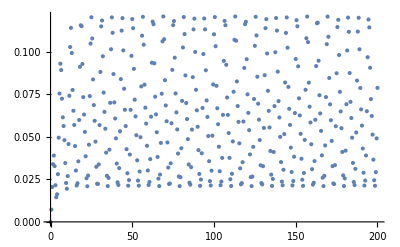
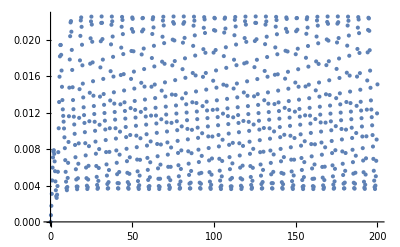
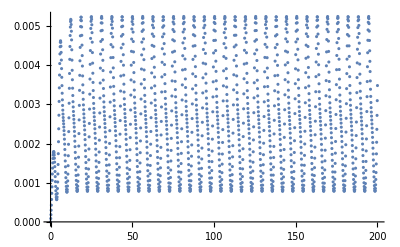
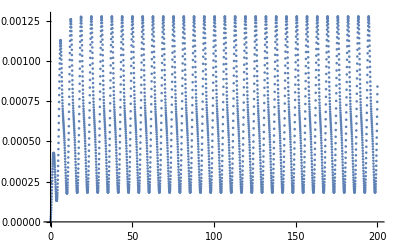

{2.42066,2.10705,2.03697}

```mathematica
rkError[0.5,makeIntegrator[rk2],4]
```

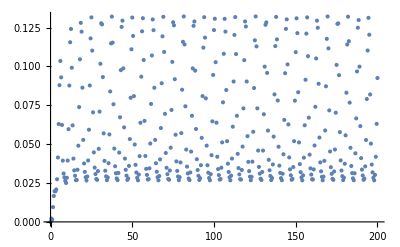
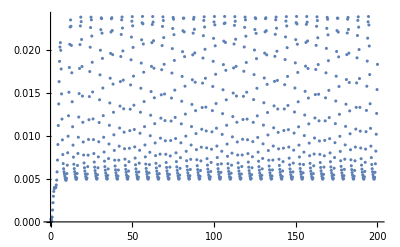
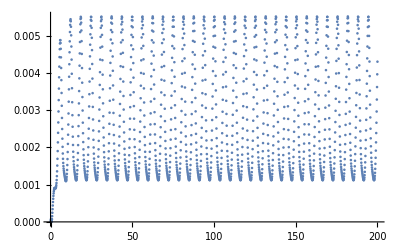
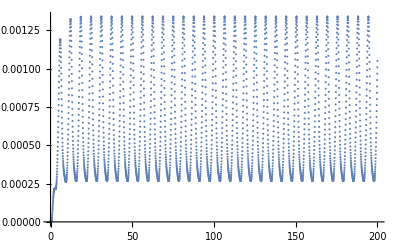

{2.46367,2.11885,2.04019}

```mathematica
rkError[0.5,makeIntegrator[vl2],4]
```